```mathematica
(*
 * Gourav Siddhad
* Btech Computer Sc. 2nd Yr
* 3235
 *)
SecantMethod[x0_,x1_,n_,f_]:=
Module[{},
xk=N[x0];xk1=N[x1];i=0;
OutputDetails={};

While[i<n,
xk2=(xk*f[xk1]-xk1*f[xk])/(f[xk1]-f[xk]);
xk=xk1;
xk1=xk2;
i++;
OutputDetails=Append[OutputDetails,{i,xk2,f[xk2]}];
];

Print[NumberForm[TableForm[OutputDetails,TableHeadings-> {None,{"i","xi","f[xi]"}}],8]];
Print[" Root After ",n," Iterations ",NumberForm[xk2,8]];
];
```

i | xi | f[xi]
1 | 0.25 | -0.234375
2 | 0.18644068 | 0.074277312
3 | 0.20173626 | -0.00047111617
4 | 0.20163985 | -8.642293×10^-7
5 | 0.20163968 | 1.0352719×10^-11
6 | 0.20163968 | -2.220446×10^-16

Root After 6 Iterations 0.20163968

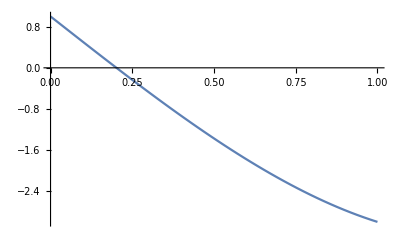

```mathematica
(* Example 1 *)
f[x_]:=x^3-5x+1
SecantMethod[0,1,6,f];
Plot[f[x],{x,0,1}]
```

i | xi | f[xi]
1 | 0.5 | 0.375
2 | 0.63636364 | 0.042824944
3 | 0.65394402 | -0.0032739053
4 | 0.65269547 | 0.00002155327
5 | 0.65270364 | 1.0540565×10^-8
6 | 0.65270364 | -3.3972825×10^-14

Root After 6 Iterations 0.65270364

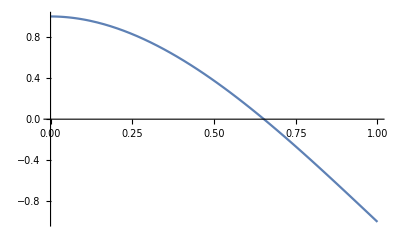

```mathematica
(* Example 2 *)
f[x_]:=x^3-3*(x^2)+1;
SecantMethod[0,1,6,f];
Plot[f[x],{x,0,1}]
```

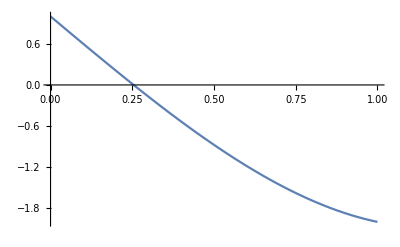

i | xi | f[xi]
1 | 0.33333333 | -0.2962963
2 | 0.2173913 | 0.14070847
3 | 0.25472276 | -0.002363704
4 | 0.25410601 | -0.000016444519
5 | 0.25410169 | 2.0474004×10^-9
6 | 0.25410169 | -1.7763568×10^-15

Root After 6 Iterations 0.25410169

```mathematica
(* Example 3 *)
f[x_]:=x^3-4*x+1
Plot[f[x],{x,0,1}]
SecantMethod[0,1,6,f]
```

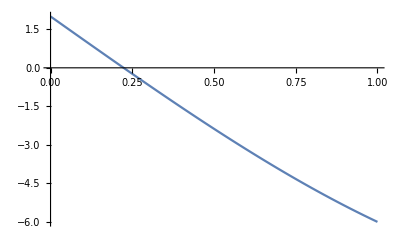

i | xi | f[xi]
1 | 0.25 | -0.234375
2 | 0.2195122 | 0.034967572
3 | 0.22347029 | -0.000072768149
4 | 0.22346207 | -2.1637519×10^-8
5 | 0.22346207 | 1.3322676×10^-14
6 | 0.22346207 | 0.

Root After 6 Iterations 0.22346207

```mathematica
(* Example 4 *)
f[x_]:=x^3-9*x+2
Plot[f[x],{x,0,1}]
SecantMethod[0,1,6,f]
```

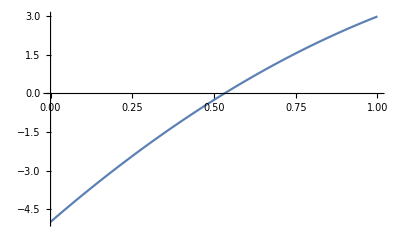

i | xi | f[xi]
1 | 0.625 | 0.703125
2 | 0.51020408 | -0.16867972
3 | 0.53241518 | 0.0061692323
4 | 0.5316315 | 0.000050376661
5 | 0.53162505 | -1.5293883×10^-8
6 | 0.53162505 | 3.7969627×10^-14

Root After 6 Iterations 0.53162505

```mathematica
(* Example 5 *)
f[x_]:=3*x^2-6*x^2+11*x-5
Plot[f[x],{x,0,1}]
SecantMethod[0,1,6,f]
```